```mathematica
Quit[]
```

Import MASS toolbox

```mathematica
<<Toolbox`
<<Toolbox`Style`
```

Define working directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Import Smallbone model

```mathematica
modelSmallbone18=biomodel2model["MODEL1303260018"];
```

See model structure (no regulation included, and please ignore the dashed arrows, they have no special meaning)

```mathematica
First@Import["glycolysis_yeast.pdf"]
```

-Graphics-

Metabolites in the model

```mathematica
modelSmallbone18["Species"]
```

{AcAld^cell,ACE^cell,ADP^cell,AMP^cell,BPG^cell,DHAP^cell,EtOH^cell,F16bP^cell,F6P^cell,G1P^cell,G3P^cell,G6P^cell,GAP^cell,GLC^cell,GLCx^extracellular,GLY^cell,NAD^cell,P2G^cell,P3G^cell,PEP^cell,PYR^cell,T6P^cell,TRH^cell,ATP^cell,NADH^cell,SUC^cell,UDG^cell,UDP^cell,UTP^cell}

Reactions in the model

```mathematica
modelSmallbone18["Reactions"]
```

{(AcAld^cell+NADH^cell⇌EtOH^cell+NAD^cell)^ADH_ADH1,(AcAld^cell+NADH^cell⇌EtOH^cell+NAD^cell)^ADH_ADH5,(2 ADP^cell⇌AMP^cell+ATP^cell)^AK,(ATP^cell→ADP^cell)^ATPase,(P2G^cell⇌PEP^cell)^ENO_ENO1,(P2G^cell⇌PEP^cell)^ENO_ENO2,(F16bP^cell⇌DHAP^cell+GAP^cell)^FBA,(DHAP^cell+NADH^cell⇌G3P^cell+NAD^cell)^GPD,(P3G^cell⇌P2G^cell)^GPM,(G3P^cell→GLY^cell)^GPP,(ATP^cell+GLC^cell⇌ADP^cell+G6P^cell)^HXK_GLK1,(ATP^cell+GLC^cell⇌ADP^cell+G6P^cell)^HXK_HXK1,(ATP^cell+GLC^cell⇌ADP^cell+G6P^cell)^HXK_HXK2,(PYR^cell→AcAld^cell)^PDC_PDC1,(PYR^cell→AcAld^cell)^PDC_PDC5,(PYR^cell→AcAld^cell)^PDC_PDC6,(ATP^cell+F6P^cell→ADP^cell+F16bP^cell)^PFK,(G6P^cell⇌F6P^cell)^PGI,(ADP^cell+BPG^cell⇌ATP^cell+P3G^cell)^PGK,(G6P^cell⇌G1P^cell)^PGM,(ADP^cell+PEP^cell⇌ATP^cell+PYR^cell)^PYK_CDC19,(ADP^cell+PEP^cell⇌ATP^cell+PYR^cell)^PYK_PYK2,(GAP^cell+NAD^cell⇌BPG^cell+NADH^cell)^TDH_TDH1,(GAP^cell+NAD^cell⇌BPG^cell+NADH^cell)^TDH_TDH2,(GAP^cell+NAD^cell⇌BPG^cell+NADH^cell)^TDH_TDH3,(DHAP^cell⇌GAP^cell)^TPI,(T6P^cell→TRH^cell)^TPP,(G6P^cell+UDG^cell→T6P^cell+UDP^cell)^TPS,(G1P^cell+UTP^cell→UDG^cell)^UGP,(AcAld^cell+NAD^cell→ACE^cell+NADH^cell)^acetate_branch,(3 NAD^cell+PYR^cell→3 NADH^cell+0.75 SUC^cell)^succinate_branch,(ATP^cell+UDP^cell→ADP^cell+UTP^cell)^udp_to_utp,(GLCx^extracellular⇌GLC^cell)^HXT}

Fluxes in the model

```mathematica
modelSmallbone18["Fluxes"]
```

{v_ADH_ADH1,v_ADH_ADH5,v_AK,v_ATPase,v_ENO_ENO1,v_ENO_ENO2,v_FBA,v_GPD,v_GPM,v_GPP,v_HXK_GLK1,v_HXK_HXK1,v_HXK_HXK2,v_PDC_PDC1,v_PDC_PDC5,v_PDC_PDC6,v_PFK,v_PGI,v_PGK,v_PGM,v_PYK_CDC19,v_PYK_PYK2,v_TDH_TDH1,v_TDH_TDH2,v_TDH_TDH3,v_TPI,v_TPP,v_TPS,v_UGP,v_acetate_branch,v_succinate_branch,v_udp_to_utp,v_HXT}

Define starveSystem function

```mathematica
starveSystem[starveTime_, starveGlc_, originalModel_] := 
 Module[{modelTemp, cSmallbone, fSmallbone},
  modelTemp = originalModel;
  {cSmallbone, fSmallbone} = 
   simulate[modelTemp, {t, 0, starveTime}, 
   Parameters -> {Toolbox`species["GLCx", "extracellular"] -> 
       starveGlc}]; 

  updateInitialConditions[modelTemp, cSmallbone /. t -> starveTime];
  Return[{modelTemp, cSmallbone, fSmallbone}];];
```

```mathematica
exportData[outputFile_,data_, simLength_, timeInterval_:0.001]:=Block[{concDataToExport},

concDataToExport = 
	Table[
		Flatten@{tPoint, Values@data/.t-> tPoint},
	{tPoint, 0, simLength, timeInterval}];

	concDataToExport=Insert[concDataToExport,Flatten@{"t", Map[getID@#&, Keys@data]},1];
	Export[outputFile, concDataToExport, "CSV"];

];
```

#### Simulate cell starvation

Define starvation time, glucose concentration during starvation, and glucose concentration for the pulse

```mathematica
starveGlc=0.1; (* in mM/L *)
starveTime=1200; (* in seconds *)
```

Starve the model, a new model is returned whose initial metabolite concentrations are the concentrations at the end of the starvation period

```mathematica
{model,concStarv, fluxStarv}=starveSystem[starveTime,starveGlc,modelSmallbone18];
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

Export simulation data

```mathematica
exportData["conc_starvation.csv", concStarv, starveTime,0.1];
exportData["flux_starvation.csv", fluxStarv, starveTime,0.1];
```

$Aborted

Plot metabolite and flux time courses during starvation

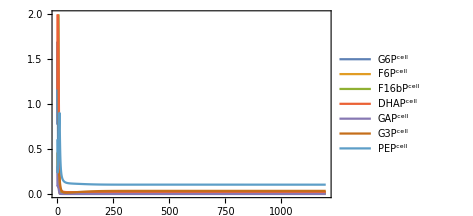

```mathematica
plotSimulation[filter[concStarv,{G6P^cell,F6P^cell,F16bP^cell, DHAP^cell,GAP^cell,G3P^cell,PEP^cell}],PlotFunction->Plot,PlotRange->{{0,1200},{0,2}},Legend->True]
```

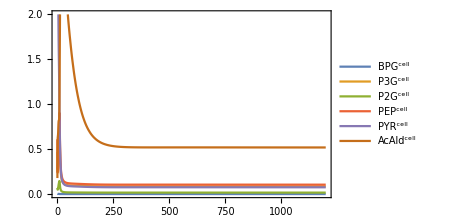

```mathematica
plotSimulation[filter[concStarv,{BPG^cell,P3G^cell,P2G^cell,PEP^cell,PYR^cell,AcAld^cell}],PlotFunction->Plot,PlotRange->{{0,1200},{0,2}},Legend->True]
```

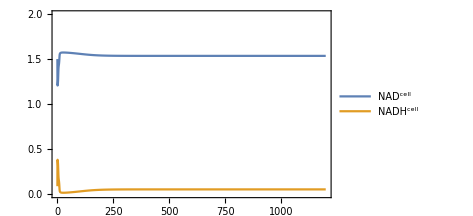

```mathematica
plotSimulation[filter[concStarv,{NAD^cell,NADH^cell}],PlotFunction->Plot,PlotRange->{{0,1200},{0,2}},
Legend->True]
```

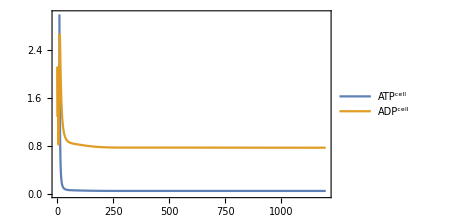

```mathematica
plotSimulation[filter[concStarv,{ATP^cell,ADP^cell}],PlotFunction->Plot,PlotRange->{{0,1200},{0,3}},Legend->True]
```

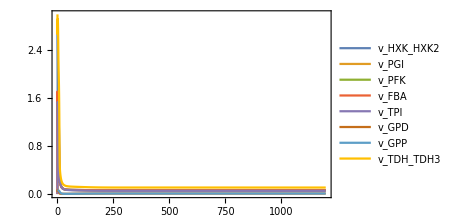

```mathematica
plotSimulation[filter[fluxStarv,{Subscript[v, HXK_HXK2],Subscript[v, PGI],Subscript[v, PFK],Subscript[v, FBA],Subscript[v, TPI],Subscript[v, GPD],Subscript[v, GPP],Subscript[v, TDH_TDH3]}],PlotFunction->Plot,PlotRange->{{0,1200},{0,3}},Legend->True]
```

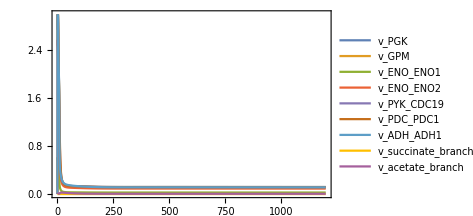

```mathematica
plotSimulation[filter[fluxStarv,{Subscript[v, PGK],Subscript[v, GPM],Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2],Subscript[v, PYK_CDC19],Subscript[v, PDC_PDC1],Subscript[v, ADH_ADH1],Subscript[v, succinate_branch],Subscript[v, acetate_branch]}],PlotFunction->Plot,PlotRange->{{0,1200},{0,3}},Legend->True]
```

#### Simulate glucose pulse, with external glucose concentration set to 4mM/mol

Simulate the model

```mathematica
{concentrationGlcPulse,fluxGlcPulse}=simulate[model,{t,0,1200},Parameters->{GLCx^extracellular->4}];ble
```

```mathematica
model["Parameters"]//TableForm
```

Keq_ADH_Global→14492.8
Keq_ENO_Global→6.7
Keq_HXK_Global→2000.
Keq_PYK_Global→6500.
Keq_TDH_Global→0.00533413
NA_Global→6.02214×10^20 per$32$mmol
sum_AXP_Global→6.02 mM
sum_NAD_Global→1.59 mM
sum_UXP_Global→1.39785 mM
volume_Global→5.×10^-15 Liter
Volume_cell→1. Liter
Volume_extracellular→1. Liter
ACE^cell→223. mmol Liter^-1
EtOH^cell→221.89 mmol Liter^-1
F26bP^cell→0.003 mmol Liter^-1
GLCx^extracellular→74. mmol Liter^-1
GLY^cell→0.15 mmol Liter^-1
SUC^cell→0. mmol Liter^-1
TRH^cell→0.0153879 mmol Liter^-1
ADH1^cell→0.163909 mmol Liter^-1
ADH5^cell→0.00424998 mmol Liter^-1
CDC19^cell→2.04839 mmol Liter^-1
ENO1^cell→0.686372 mmol Liter^-1
ENO2^cell→1.97445 mmol Liter^-1
FBA1^cell→1.33839 mmol Liter^-1
GLK1^cell→0.045087 mmol Liter^-1
GPD1^cell→0.00683511 mmol Liter^-1
GPD2^cell→0.000793406 mmol Liter^-1
GPM1^cell→0.73 mmol Liter^-1
HOR2^cell→0.00547347 mmol Liter^-1
HXK1^cell→0.0167807 mmol Liter^-1
HXK2^cell→0.0613314 mmol Liter^-1
PDC1^cell→1.06781 mmol Liter^-1
PDC5^cell→0.0123547 mmol Liter^-1
PDC6^cell→0.00654086 mmol Liter^-1
PFK1^cell→0.046785 mmol Liter^-1
PFK2^cell→0.0390366 mmol Liter^-1
PGI1^cell→0.138291 mmol Liter^-1
PGK1^cell→0.257657 mmol Liter^-1
PGM1^cell→0.0032623 mmol Liter^-1
PGM2^cell→0.00125869 mmol Liter^-1
PYK2^cell→0.00606994 mmol Liter^-1
RHR2^cell→0.0511805 mmol Liter^-1
TDH1^cell→0.350865 mmol Liter^-1
TDH2^cell→0. mmol Liter^-1
TDH3^cell→4.2044 mmol Liter^-1
TPI1^cell→0.294358 mmol Liter^-1
TPS1^cell→0.00339248 mmol Liter^-1
TPS2^cell→0.00265985 mmol Liter^-1
UGP1^cell→0.00620211 mmol Liter^-1
kcat_ADH_ADH1→176. per$32$second
Ketoh_ADH_ADH1→17. mM
Kinad_ADH_ADH1→0.92 mM
Knad_ADH_ADH1→0.17 mM
Knadh_ADH_ADH1→0.11 mM
Kinadh_ADH_ADH1→0.031 mM
Kacald_ADH_ADH1→0.4622 mM
Kiacald_ADH_ADH1→1.1 mM
Kietoh_ADH_ADH1→90. mM
kcat_ADH_ADH5→0. per$32$second
Ketoh_ADH_ADH5→17. mM
Kinad_ADH_ADH5→0.92 mM
Knad_ADH_ADH5→0.17 mM
Knadh_ADH_ADH5→0.11 mM
Kinadh_ADH_ADH5→0.031 mM
Kacald_ADH_ADH5→1.11 mM
Kiacald_ADH_ADH5→1.1 mM
Kietoh_ADH_ADH5→90. mM
k_AK→0.75 per$32$mM$32$per$32$second
Keq_AK→0.45
Vmax_ATPase→6.16 mM$32$per$32$second
Katp_ATPase→3. mM
kcat_ENO_ENO1→7.6 per$32$second
Kp2g_ENO_ENO1→0.043 mM
Kpep_ENO_ENO1→0.5 mM
kcat_ENO_ENO2→19.87 per$32$second
Kp2g_ENO_ENO2→0.104 mM
Kpep_ENO_ENO2→0.5 mM
kcat_FBA→4.139 per$32$second
Kf16bp_FBA→0.4507 mM
Keq_FBA→0.069 mM
Kdhap_FBA→2. mM
Kgap_FBA→2.4 mM
Kigap_FBA→10. mM
Vmax_GPD→0.783333 mM$32$per$32$second
Knadh_GPD→0.023 mM
Kdhap_GPD→0.54 mM
Keq_GPD→10000.
Kfbp_GPD→4.8 mM
Katp_GPD→0.73 mM
Kadp_GPD→2. mM
Knad_GPD→0.93 mM
Kg3p_GPD→1.2 mM
kcat_GPM→400. per$32$second
Kp3g_GPM→1.2 mM
Keq_GPM→0.19
Kp2g_GPM→1.41 mM
Vmax_GPP→0.883333 mM$32$per$32$second
Kg3p_GPP→3.5 mM
kcat_HXK_GLK1→0.0721 per$32$second
Kglc_HXK_GLK1→0.0106 mM
Katp_HXK_GLK1→0.865 mM
Kg6p_HXK_GLK1→30. mM
Kadp_HXK_GLK1→0.23 mM
kcat_HXK_HXK1→10.2 per$32$second
Kglc_HXK_HXK1→0.15 mM
Katp_HXK_HXK1→0.293 mM
Kg6p_HXK_HXK1→30. mM
Kadp_HXK_HXK1→0.23 mM
Kit6p_HXK_HXK1→0.2 mM
kcat_HXK_HXK2→63.1 per$32$second
Kglc_HXK_HXK2→0.2 mM
Katp_HXK_HXK2→0.195 mM
Kg6p_HXK_HXK2→30. mM
Kadp_HXK_HXK2→0.23 mM
Kit6p_HXK_HXK2→0.04 mM
kcat_PDC_PDC1→12.14 per$32$second
Kpyr_PDC_PDC1→8.5 mM
kcat_PDC_PDC5→10.32 per$32$second
Kpyr_PDC_PDC5→7.08 mM
kcat_PDC_PDC6→9.21 per$32$second
Kpyr_PDC_PDC6→2.92 mM
kcat_PFK→209.6 per$32$second
gR_PFK→5.12
Kf6p_PFK→0.1 mM
Katp_PFK→0.71 mM
L0_PFK→0.66
Ciatp_PFK→100.
Kiatp_PFK→0.65 mM
Camp_PFK→0.0845
Kamp_PFK→0.0995 mM
Cf26_PFK→0.0174
Kf26_PFK→0.000682 mM
Cf16_PFK→0.397
Kf16_PFK→0.111 mM
Catp_PFK→3.
Kadp_PFK→1. mM
Keq_PFK→800.
kcat_PGI→487.36 per$32$second
Kg6p_PGI→1.0257 mM
Keq_PGI→0.29
Kf6p_PGI→0.307 mM
kcat_PGK→58.6 per$32$second
Keq_PGK→3200.
Kp3g_PGK→4.58 mM
Katp_PGK→1.99 mM
Kbpg_PGK→0.003 mM
Kadp_PGK→0.2 mM
nHadp_PGK→2.
Vmax_PGM→0.12762 mM$32$per$32$second
Kg6p_PGM→0.05 mM
Kg1p_PGM→0.023 mM
Keq_PGM→0.1667
kcat_PYK_CDC19→20.146 per$32$second
Kpep_PYK_CDC19→0.281 mM
Kadp_PYK_CDC19→0.243 mM
Kpyr_PYK_CDC19→21. mM
Katp_PYK_CDC19→1.5 mM
Kiatp_PYK_CDC19→9.3 mM
Kf16p_PYK_CDC19→0.2 mM
L0_PYK_CDC19→100.
kcat_PYK_PYK2→0. per$32$second
Kpep_PYK_PYK2→0.19 mM
Kadp_PYK_PYK2→0.3 mM
Kpyr_PYK_PYK2→21. mM
Katp_PYK_PYK2→1.5 mM
Kiatp_PYK_PYK2→9.3 mM
Kf16p_PYK_PYK2→0.2 mM
L0_PYK_PYK2→100.
kcat_TDH_TDH1→19.12 per$32$second
Kgap_TDH_TDH1→0.495 mM
Knad_TDH_TDH1→0.09 mM
Kbpg_TDH_TDH1→0.0098 mM
Knadh_TDH_TDH1→0.06 mM
kcat_TDH_TDH2→8.633 per$32$second
Kgap_TDH_TDH2→0.77 mM
Knad_TDH_TDH2→0.09 mM
Kbpg_TDH_TDH2→0.0098 mM
Knadh_TDH_TDH2→0.06 mM
kcat_TDH_TDH3→18.162 per$32$second
Kgap_TDH_TDH3→0.423 mM
Knad_TDH_TDH3→0.09 mM
Kbpg_TDH_TDH3→0.909 mM
Knadh_TDH_TDH3→0.06 mM
kcat_TPI→564.38 per$32$second
Kdhap_TPI→6.454 mM
Kgap_TPI→5.25 mM
Kigap_TPI→35.1 mM
Keq_TPI→0.045
Vmax_TPP→2.34 mM$32$per$32$second
Kt6p_TPP→0.5 mM
Vmax_TPS→0.49356 mM$32$per$32$second
Kg6p_TPS→3.8 mM
Kudg_TPS→0.886 mM
Vmax_UGP→13.2552 mM$32$per$32$second
Kutp_UGP→0.11 mM
Kiutp_UGP→0.11 mM
Kg1p_UGP→0.32 mM
Kiudg_UGP→0.0035 mM
k_acetate_branch→0.0055434 per$32$mM$32$per$32$second
k_succinate_branch→0. per$32$mM$32$per$32$second
k_udp_to_utp→0.0745258 per$32$mM$32$per$32$second
Vmax_HXT→3.35 mM$32$per$32$second
Kglc_HXT→0.9 mM
Ki_HXT→0.91

Export simulation data

```mathematica
exportData["conc_glc_pulse.csv", concentrationGlcPulse, 60,0.01];
exportData["flux_glc_pulse.csv", fluxGlcPulse, 60,0.01];
```

Plot initial metabolite concentrations, to see which metabolites accumulated during starvation

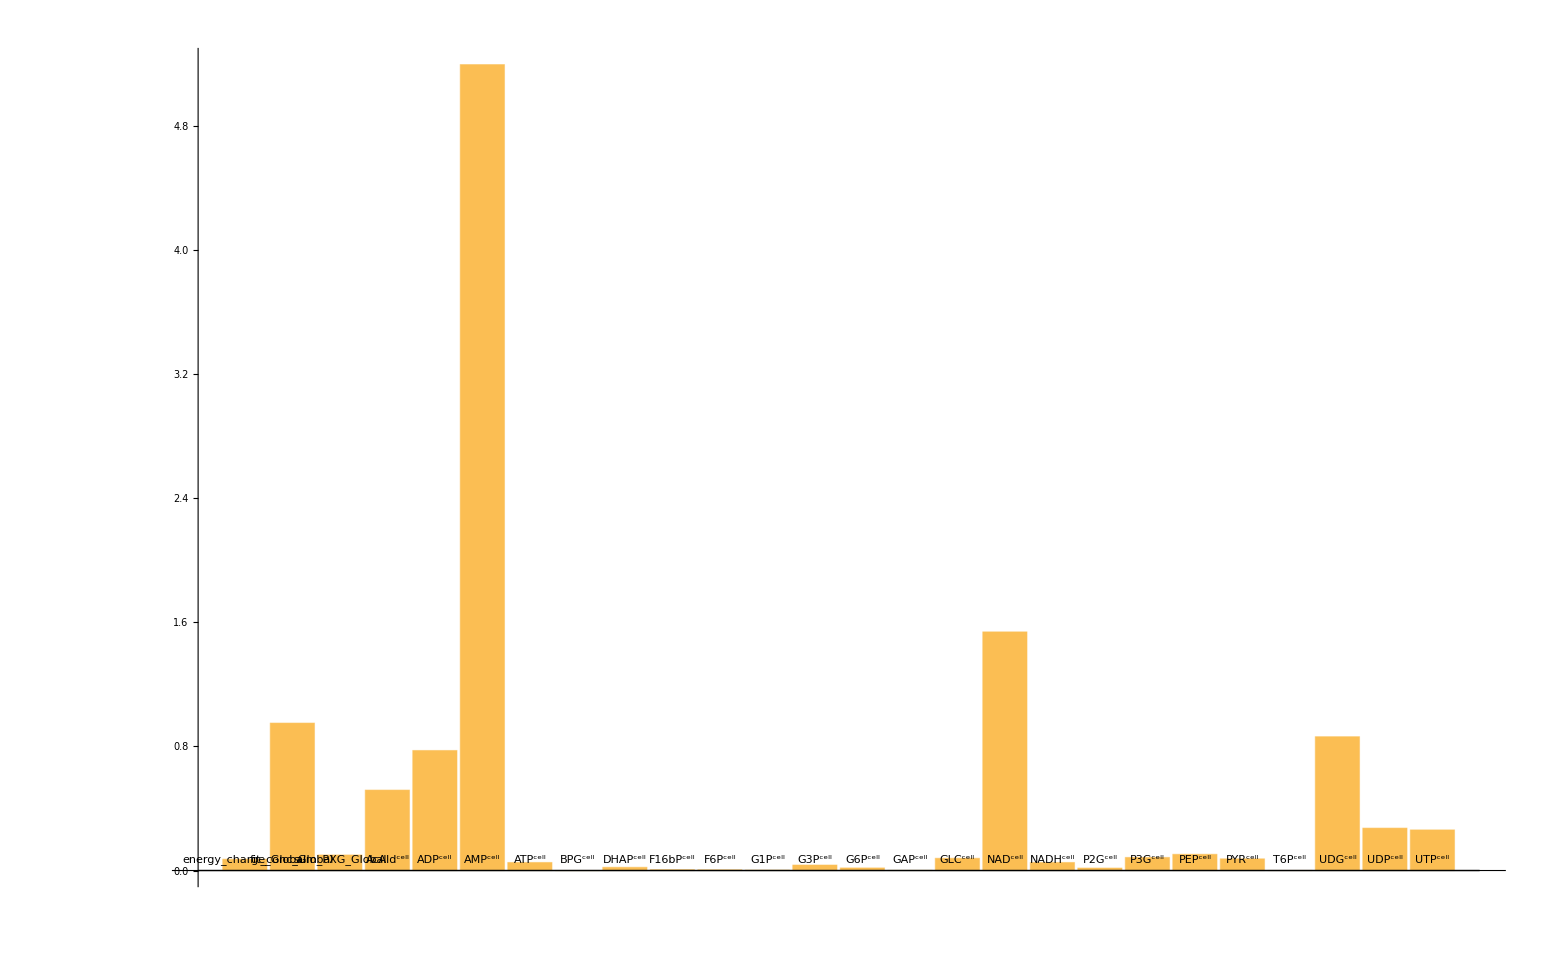

```mathematica
BarChart[Values@model["InitialConditions"], ChartLabels->Placed[Keys@model["InitialConditions"], Bottom]]
```

Plot simulation results

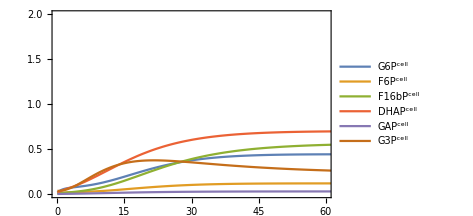

```mathematica
plot=plotSimulation[filter[concentrationGlcPulse,{G6P^cell,F6P^cell,F16bP^cell, DHAP^cell,GAP^cell,G3P^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
Export["glc_pulse_conc1.pdf", plot];
```

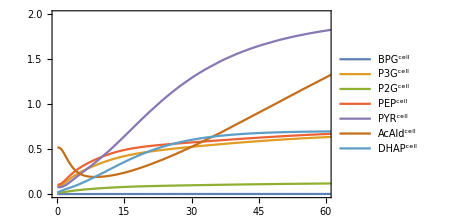

```mathematica
plot=plotSimulation[filter[concentrationGlcPulse,{BPG^cell,P3G^cell,P2G^cell,PEP^cell,PYR^cell,AcAld^cell,DHAP^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
Export["glc_pulse_conc2.pdf", plot];
```

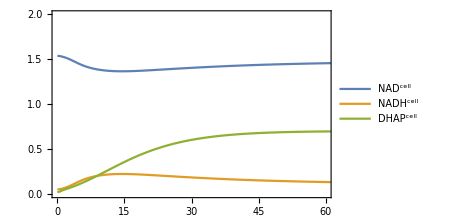

```mathematica
plot=plotSimulation[filter[concentrationGlcPulse,{NAD^cell,NADH^cell,DHAP^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
Export["glc_pulse_cofactors1.pdf", plot];
```

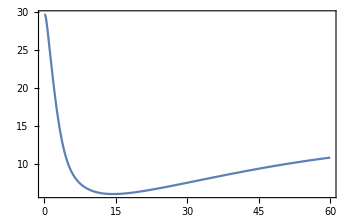

```mathematica
plot=Plot[Values@filter[concentrationGlcPulse,{NAD^cell}]/Values@filter[concentrationGlcPulse,{NADH^cell}], {t,0,60}]
Export["glc_pulse_NADratio.pdf", plot];
```

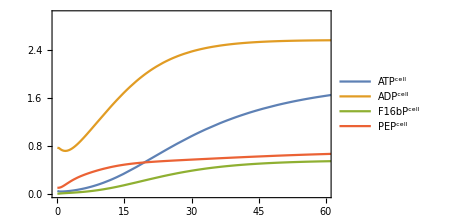

```mathematica
plot=plotSimulation[filter[concentrationGlcPulse,{ATP^cell,ADP^cell,F16bP^cell,PEP^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
Export["glc_pulse_cofactors2.pdf", plot];
```

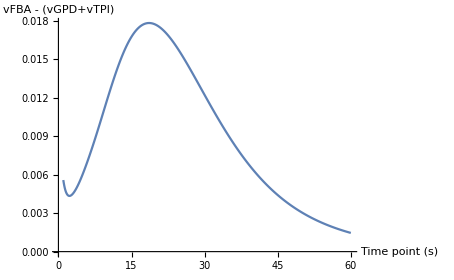

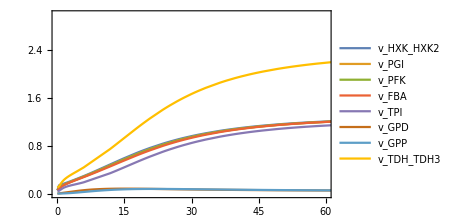

```mathematica
plot=plotSimulation[filter[fluxGlcPulse,{Subscript[v, HXK_HXK2],Subscript[v, PGI],Subscript[v, PFK],Subscript[v, FBA],Subscript[v, TPI],Subscript[v, GPD],Subscript[v, GPP],Subscript[v, TDH_TDH3]}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
Export["glc_pulse_flux1.pdf", plot];
```

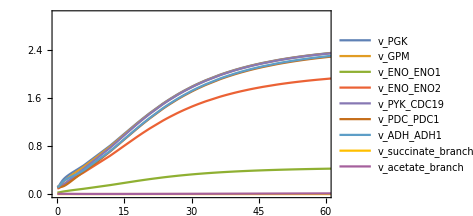

```mathematica
plot=plotSimulation[filter[fluxGlcPulse,{Subscript[v, PGK],Subscript[v, GPM],Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2],Subscript[v, PYK_CDC19],Subscript[v, PDC_PDC1],Subscript[v, ADH_ADH1],Subscript[v, succinate_branch],Subscript[v, acetate_branch]}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
Export["glc_pulse_flux2.pdf", plot];
```

#### Simulate first glucose and acetaldehyde coinjection, with external glucose concentration set to 4 mM/mol and internal acetadehyde concentration set to 2.3 mM/L

Simulate the model

```mathematica
{concentrationCoinjection1,fluxCoinjection1}=simulate[model,{t,0,120},Parameters->{GLCx^extracellular->4}, InitialConditions->{ AcAld^cell-> 2.3}];
```

Export simulation data

```mathematica
exportData["conc_glc_acald23.csv", concentrationCoinjection1, 60,0.01];
exportData["flux_glc_acald23.csv", fluxCoinjection1, 60,0.01];
```

Plot simulation results

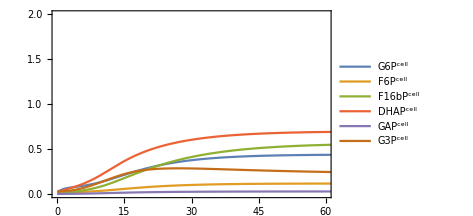

```mathematica
plot=plotSimulation[filter[concentrationCoinjection1,{G6P^cell,F6P^cell,F16bP^cell, DHAP^cell,GAP^cell,G3P^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
Export["glc_acald2_3_conc1.pdf", plot];
```

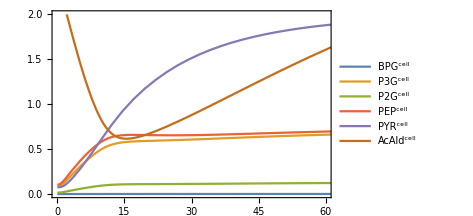

```mathematica
plot=plotSimulation[filter[concentrationCoinjection1,{BPG^cell,P3G^cell,P2G^cell,PEP^cell,PYR^cell,AcAld^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
Export["glc_acald2_3_conc2.pdf", plot];
```

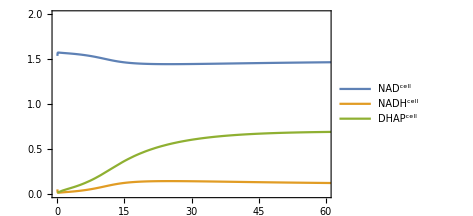

```mathematica
plot=plotSimulation[filter[concentrationCoinjection1,{NAD^cell,NADH^cell,DHAP^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
Export["glc_acald2_3_cofactors1.pdf", plot];
```

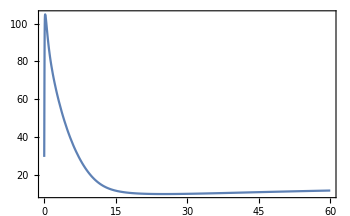

```mathematica
plot=Plot[Values@filter[concentrationCoinjection1,{NAD^cell}]/Values@filter[concentrationCoinjection1,{NADH^cell}], {t,0,60}]
Export["glc_acald2_3_NADratio.pdf", plot];
```

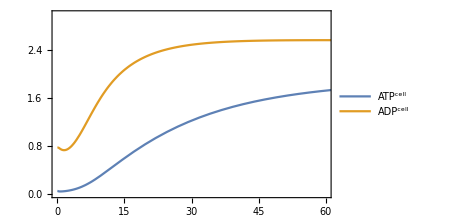

```mathematica
plot=plotSimulation[filter[concentrationCoinjection1,{ATP^cell,ADP^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
Export["glc_acald2_3_cofactors2.pdf", plot];
```

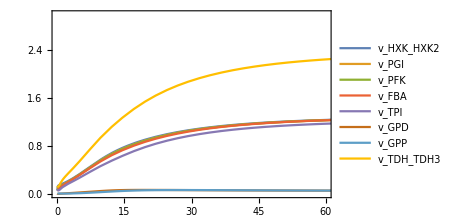

```mathematica
plot=plotSimulation[filter[fluxCoinjection1,{Subscript[v, HXK_HXK2],Subscript[v, PGI],Subscript[v, PFK],Subscript[v, FBA],Subscript[v, TPI],Subscript[v, GPD],Subscript[v, GPP],Subscript[v, TDH_TDH3]}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
Export["glc_acald2_3_flux1.pdf", plot];
```

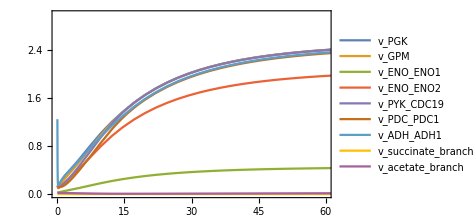

```mathematica
plot=plotSimulation[filter[fluxCoinjection1,{Subscript[v, PGK],Subscript[v, GPM],Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2],Subscript[v, PYK_CDC19],Subscript[v, PDC_PDC1],Subscript[v, ADH_ADH1],Subscript[v, succinate_branch],Subscript[v, acetate_branch]}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
Export["glc_acald2_3_flux2.pdf", plot];
```

#### Simulate second glucose and acetaldehyde coinjection, with external glucose concentration set to 4 mM/mol and internal acetadehyde concentration set to 12 mM/L

Simulate the model

```mathematica
{concentrationCoinjection2,fluxCoinjection2}=simulate[model,{t,0,120},Parameters->{Toolbox`species["GLCx","extracellular"]->4}, InitialConditions->{ AcAld^cell-> 12}];
```

Export simulation data

```mathematica
exportData["conc_glc_acald12.csv", concentrationCoinjection2, 60,0.01];
exportData["flux_glc_acald12.csv", fluxCoinjection2, 60,0.01];
```

Plot results during starvation

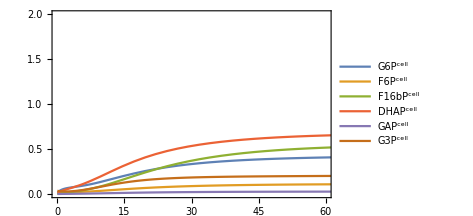

```mathematica
plot=plotSimulation[filter[concentrationCoinjection2,{G6P^cell,F6P^cell,F16bP^cell, DHAP^cell,GAP^cell,G3P^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
Export["glc_acald12_conc1.pdf", plot];
```

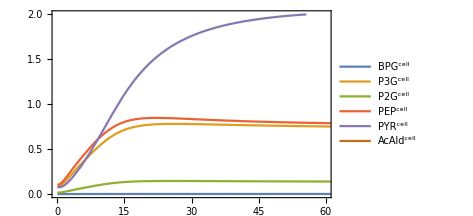

```mathematica
plot=plotSimulation[filter[concentrationCoinjection2,{BPG^cell,P3G^cell,P2G^cell,PEP^cell,PYR^cell,AcAld^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
Export["glc_acald12_conc2.pdf", plot];
```

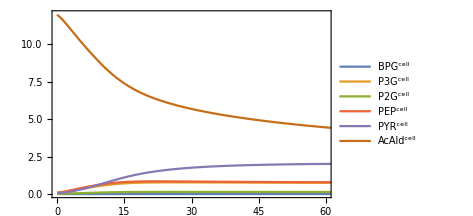

```mathematica
plot=plotSimulation[filter[concentrationCoinjection2,{BPG^cell,P3G^cell,P2G^cell,PEP^cell,PYR^cell,AcAld^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,12}},Legend->True]
Export["glc_acald12_conc2.pdf", plot];
```

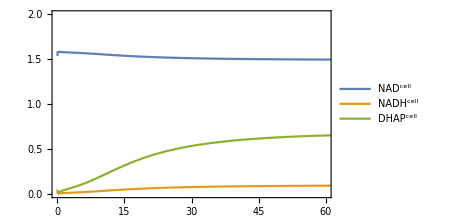

```mathematica
plot=plotSimulation[filter[concentrationCoinjection2,{NAD^cell,NADH^cell,DHAP^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
Export["glc_acald12_cofactors1.pdf", plot];
```

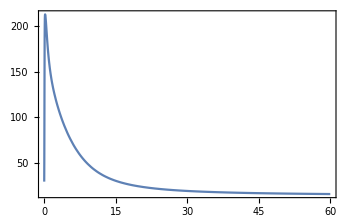

```mathematica
plot=Plot[Values@filter[concentrationCoinjection2,{NAD^cell}]/Values@filter[concentrationCoinjection2,{NADH^cell}], {t,0,60}]
Export["glc_acald12_NADratio.pdf", plot];
```

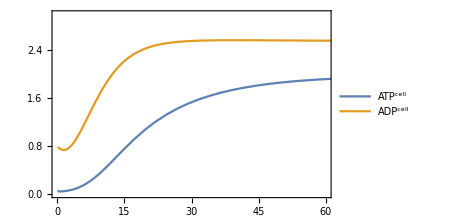

```mathematica
plot=plotSimulation[filter[concentrationCoinjection2,{ATP^cell,ADP^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
Export["glc_acald12_cofactors2.pdf", plot];
```

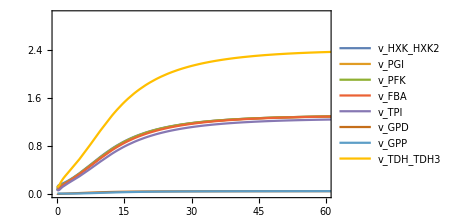

```mathematica
plot=plotSimulation[filter[fluxCoinjection2,{Subscript[v, HXK_HXK2],Subscript[v, PGI],Subscript[v, PFK],Subscript[v, FBA],Subscript[v, TPI],Subscript[v, GPD],Subscript[v, GPP],Subscript[v, TDH_TDH3]}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
Export["glc_acald12_flux1.pdf", plot];
```

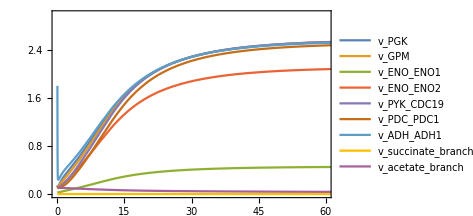

```mathematica
plot=plotSimulation[filter[fluxCoinjection2,{Subscript[v, PGK],Subscript[v, GPM],Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2],Subscript[v, PYK_CDC19],Subscript[v, PDC_PDC1],Subscript[v, ADH_ADH1],Subscript[v, succinate_branch],Subscript[v, acetate_branch]}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
Export["glc_acald12_flux2.pdf", plot];
```

#### Simulate glucose pulse and addition of ethanol (duplicate concentration)

Simulate the model

```mathematica
{concentrationEthanolIncrease,fluxEthanolIncrease}=simulate[model,{t,0,120},Parameters->{GLCx^extracellular->4,EtOH^cell-> 221.89*1.5 }];
```

```mathematica
exportData["conc_glc_ethanol.csv", concentrationCoinjection2, 60,0.01];
exportData["flux_glc_ethanol.csv", fluxCoinjection2, 60,0.01];
```

Plot results during starvation

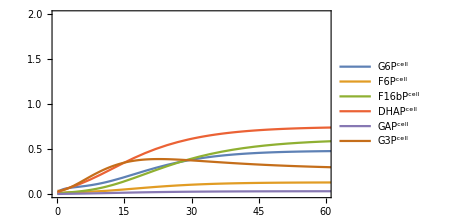

```mathematica
plot=plotSimulation[filter[concentrationEthanolIncrease,{G6P^cell,F6P^cell,F16bP^cell, DHAP^cell,GAP^cell,G3P^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
Export["glc_ethanol_conc1.pdf", plot];
```

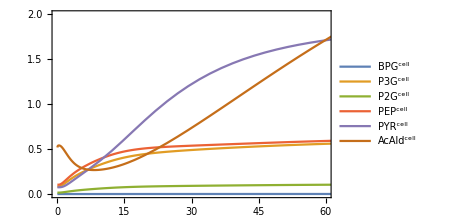

```mathematica
plot=plotSimulation[filter[concentrationEthanolIncrease,{BPG^cell,P3G^cell,P2G^cell,PEP^cell,PYR^cell,AcAld^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
Export["glc_ethanol_conc2.pdf", plot];
```

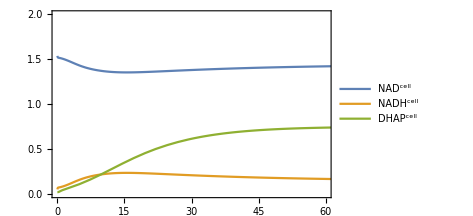

```mathematica
plot=plotSimulation[filter[concentrationEthanolIncrease,{NAD^cell,NADH^cell,DHAP^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
Export["glc_ethanol_cofactors1.pdf", plot];
```

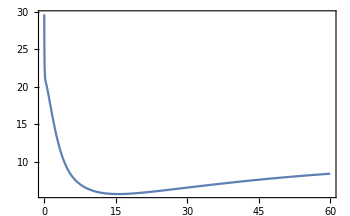

```mathematica
plot=Plot[Values@filter[concentrationEthanolIncrease,{NAD^cell}]/Values@filter[concentrationEthanolIncrease,{NADH^cell}], {t,0,60}]
Export["glc_ethanol_NADratio.pdf", plot];
```

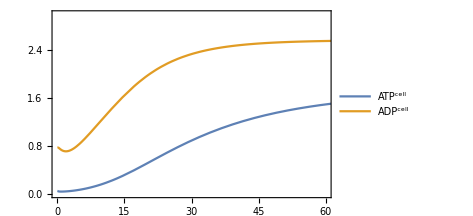

```mathematica
plot=plotSimulation[filter[concentrationEthanolIncrease,{ATP^cell,ADP^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
Export["glc_ethanol_cofactors2.pdf", plot];
```

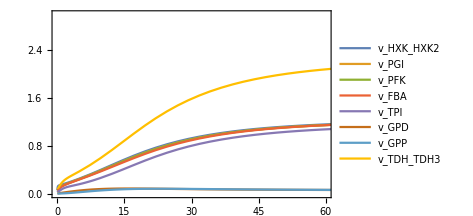

```mathematica
plot=plotSimulation[filter[fluxEthanolIncrease,{Subscript[v, HXK_HXK2],Subscript[v, PGI],Subscript[v, PFK],Subscript[v, FBA],Subscript[v, TPI],Subscript[v, GPD],Subscript[v, GPP],Subscript[v, TDH_TDH3]}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
Export["glc_ethanol_flux1.pdf", plot];
```

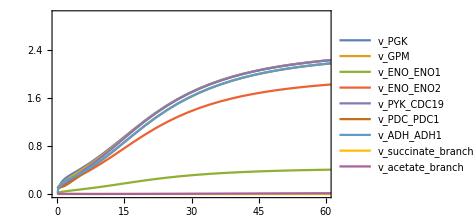

```mathematica
plot=plotSimulation[filter[fluxEthanolIncrease,{Subscript[v, PGK],Subscript[v, GPM],Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2],Subscript[v, PYK_CDC19],Subscript[v, PDC_PDC1],Subscript[v, ADH_ADH1],Subscript[v, succinate_branch],Subscript[v, acetate_branch]}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
Export["glc_ethanol_flux2.pdf", plot];
```

### Comparative plots across experiments

#### DHAP

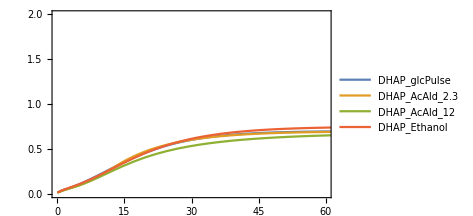

```mathematica
dhapComparisonPlot=plotSimulation[Flatten@{filter[concentrationGlcPulse,{ DHAP^cell}]/.{DHAP^cell-> "DHAP_glcPulse"},
filter[concentrationCoinjection1,{ DHAP^cell}]/.{ DHAP^cell->  "DHAP_AcAld_2.3"},
filter[concentrationCoinjection2,{ DHAP^cell}]/.{ DHAP^cell->  "DHAP_AcAld_12"},
filter[concentrationEthanolIncrease,{ DHAP^cell}]/.{ DHAP^cell-> "DHAP_Ethanol"}},
PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
```

```mathematica
Export["DHAP_across_conditions.pdf", dhapComparisonPlot];
```

#### P3G

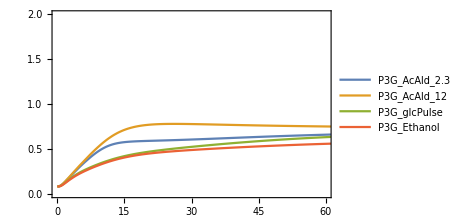

```mathematica
p3gComparisonPlot=plotSimulation[Flatten@{
filter[concentrationCoinjection1,{ P3G^cell}]/.{P3G^cell-> "P3G_AcAld_2.3"},
filter[concentrationCoinjection2,{ P3G^cell}]/.{ P3G^cell->  "P3G_AcAld_12"},
filter[concentrationGlcPulse,{ P3G^cell}]/.{P3G^cell->"P3G_glcPulse"},
filter[concentrationEthanolIncrease,{ P3G^cell}]/.{P3G^cell-> "P3G_Ethanol"}},PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
```

```mathematica
Export["3PG_across_conditions.pdf", p3gComparisonPlot];
```

#### P2G

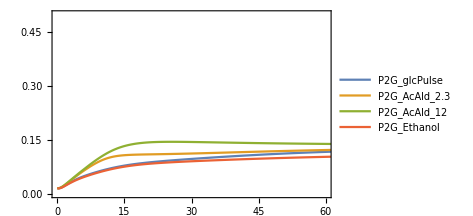

```mathematica
p2gComparisonPlot=plotSimulation[Flatten@{
filter[concentrationGlcPulse,{ P2G^cell}]/.{P2G^cell->"P2G_glcPulse"},
filter[concentrationCoinjection1,{ P2G^cell}]/.{P2G^cell-> "P2G_AcAld_2.3"},
filter[concentrationCoinjection2,{ P2G^cell}]/.{ P2G^cell->  "P2G_AcAld_12"},

filter[concentrationEthanolIncrease,{ P2G^cell}]/.{P2G^cell-> "P2G_Ethanol"}},PlotFunction->Plot,PlotRange->{{0,60},{0,0.5}},Legend->True]
```

```mathematica
Export["P2G_across_conditions.pdf", p2gComparisonPlot];
```

#### PEP

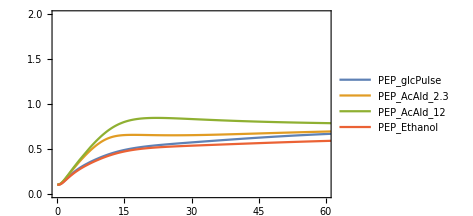

```mathematica
pepComparisonPlot=plotSimulation[Flatten@{
filter[concentrationGlcPulse,{ PEP^cell}]/.{PEP^cell->"PEP_glcPulse"},
filter[concentrationCoinjection1,{ PEP^cell}]/.{PEP^cell-> "PEP_AcAld_2.3"},
filter[concentrationCoinjection2,{ PEP^cell}]/.{ PEP^cell->  "PEP_AcAld_12"},

filter[concentrationEthanolIncrease,{ PEP^cell}]/.{PEP^cell-> "PEP_Ethanol"}},PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
```

```mathematica
Export["PEP_across_conditions.pdf", pepComparisonPlot];
```

#### PYR

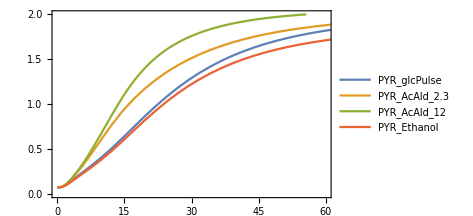

```mathematica
pyrComparisonPlot=plotSimulation[Flatten@{
filter[concentrationGlcPulse,{ PYR^cell}]/.{PYR^cell->"PYR_glcPulse"},
filter[concentrationCoinjection1,{ PYR^cell}]/.{PYR^cell-> "PYR_AcAld_2.3"},
filter[concentrationCoinjection2,{ PYR^cell}]/.{ PYR^cell->  "PYR_AcAld_12"},

filter[concentrationEthanolIncrease,{ PYR^cell}]/.{PYR^cell-> "PYR_Ethanol"}},PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
```

```mathematica
Export["PYR_across_conditions.pdf", pyrComparisonPlot];
```

#### GAP

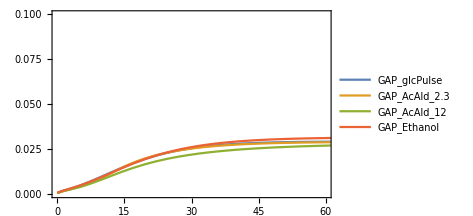

```mathematica
gapComparisonPlot=plotSimulation[Flatten@{
filter[concentrationGlcPulse,{ GAP^cell}]/.{GAP^cell->"GAP_glcPulse"},
filter[concentrationCoinjection1,{ GAP^cell}]/.{GAP^cell-> "GAP_AcAld_2.3"},
filter[concentrationCoinjection2,{ GAP^cell}]/.{ GAP^cell->  "GAP_AcAld_12"},

filter[concentrationEthanolIncrease,{ GAP^cell}]/.{GAP^cell-> "GAP_Ethanol"}},PlotFunction->Plot,PlotRange->{{0,60},{0,0.1}},Legend->True]
```

```mathematica
Export["GAP_across_conditions.pdf", gapComparisonPlot];
```

#### BPG

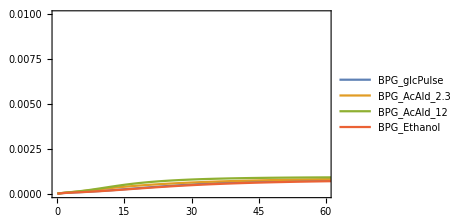

```mathematica
bpgComparisonPlot=plotSimulation[Flatten@{
filter[concentrationGlcPulse,{ BPG^cell}]/.{BPG^cell->"BPG_glcPulse"},
filter[concentrationCoinjection1,{ BPG^cell}]/.{BPG^cell-> "BPG_AcAld_2.3"},
filter[concentrationCoinjection2,{ BPG^cell}]/.{ BPG^cell->  "BPG_AcAld_12"},

filter[concentrationEthanolIncrease,{ BPG^cell}]/.{BPG^cell-> "BPG_Ethanol"}},PlotFunction->Plot,PlotRange->{{0,60},{0,0.01}},Legend->True]
```

```mathematica
Export["BPG_across_conditions.pdf", bpgComparisonPlot];
```

### Flux differences check

```mathematica
DHAPreactions=Table[

If[MemberQ[getSubstrates[rxn], DHAP^cell]||  MemberQ[getProducts[rxn],DHAP^cell],
	rxn],
{rxn,modelSmallbone18["Reactions"]}];
DHAPreactions=DeleteCases[DHAPreactions, Null]
```

{(F16bP^cell⇌DHAP^cell+GAP^cell)^FBA,(DHAP^cell+NADH^cell⇌G3P^cell+NAD^cell)^GPD,(DHAP^cell⇌GAP^cell)^TPI}

```mathematica
modelSmallbone18["Fluxes"]
```

{v_ADH_ADH1,v_ADH_ADH5,v_AK,v_ATPase,v_ENO_ENO1,v_ENO_ENO2,v_FBA,v_GPD,v_GPM,v_GPP,v_HXK_GLK1,v_HXK_HXK1,v_HXK_HXK2,v_PDC_PDC1,v_PDC_PDC5,v_PDC_PDC6,v_PFK,v_PGI,v_PGK,v_PGM,v_PYK_CDC19,v_PYK_PYK2,v_TDH_TDH1,v_TDH_TDH2,v_TDH_TDH3,v_TPI,v_TPP,v_TPS,v_UGP,v_acetate_branch,v_succinate_branch,v_udp_to_utp,v_HXT}

#### PFK - FBA

```mathematica
tList=Range[1,60,0.01];
vPFKvFBAGlcPulse = Table[(Values@FilterRules[fluxGlcPulse,{Subscript[v, PFK]}]/.t-> tPoint)-(Values@FilterRules[fluxGlcPulse,{Subscript[v, FBA]}]/.t-> tPoint),
{tPoint,tList}]//Flatten;
vPFKvFBAAcAld1 = Table[(Values@FilterRules[fluxCoinjection1,{Subscript[v, PFK]}]/.t-> tPoint)-(Values@FilterRules[fluxGlcPulse,{Subscript[v, FBA]}]/.t-> tPoint),
{tPoint,tList}]//Flatten;
vPFKvFBAAcAld2 = Table[(Values@FilterRules[fluxCoinjection2,{Subscript[v, PFK]}]/.t-> tPoint)-(Values@FilterRules[fluxGlcPulse,{Subscript[v, FBA]}]/.t-> tPoint),
{tPoint,tList}]//Flatten;
vPFKvFBAEthanol = Table[(Values@FilterRules[fluxEthanolIncrease,{Subscript[v, PFK]}]/.t-> tPoint)-(Values@FilterRules[fluxGlcPulse,{Subscript[v, FBA]}]/.t-> tPoint),
{tPoint,tList}]//Flatten;
```

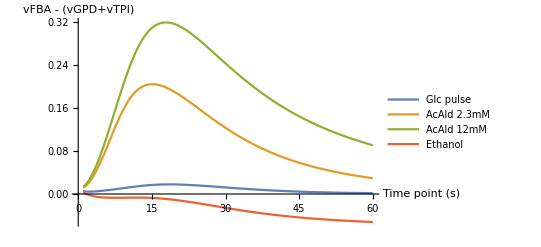

```mathematica
PFKvsFBAplot=ListLinePlot[{MapThread[{#1,#2}&,{tList, vPFKvFBAGlcPulse}],
			MapThread[{#1,#2}&,{tList, vPFKvFBAAcAld1}],
			MapThread[{#1,#2}&,{tList, vPFKvFBAAcAld2}],
			MapThread[{#1,#2}&,{tList, vPFKvFBAEthanol}]},
PlotLegends->{"Glc pulse","AcAld 2.3mM","AcAld 12mM", "Ethanol"},
AxesLabel->{"Time point (s)","vFBA - (vGPD+vTPI)"},AxesOrigin->{0,0}]
```

```mathematica
Export["vPFK_-_vFBA.pdf", PFKvsFBAplot];
```

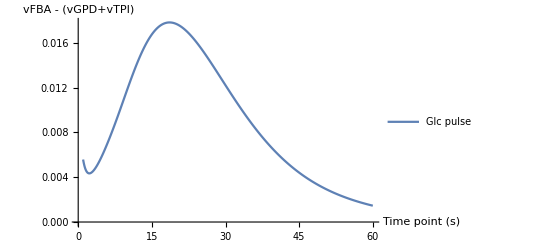

```mathematica
FBAvsGPDTPIplot=ListLinePlot[MapThread[{#1,#2}&,{tList, vPFKvFBAGlcPulse}],
PlotLegends->{"Glc pulse"},
AxesLabel->{"Time point (s)","vFBA - (vGPD+vTPI)"},AxesOrigin->{0,0}]
```

```mathematica
Export["vFBA_-_vGPD+vTPI_data.csv", FBAvsGPDTPIplot, "CSV"];
```

#### FBA - (GPD+TPI)

```mathematica
tList=Range[1,60,0.01];
vFBAvsvGPDvTPIGlcPulse = Table[(Values@FilterRules[fluxGlcPulse,{Subscript[v, FBA]}]/.t-> tPoint)-Total[Values@FilterRules[fluxGlcPulse,{Subscript[v, GPD],Subscript[v, TPI]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
vFBAvsvGPDvTPIAcAld1 = Table[(Values@FilterRules[fluxCoinjection1,{Subscript[v, FBA]}]/.t-> tPoint)-Total[Values@FilterRules[fluxCoinjection1,{Subscript[v, GPD],Subscript[v, TPI]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
vFBAvsvGPDvTPIAcAld2 = Table[(Values@FilterRules[fluxCoinjection2,{Subscript[v, FBA]}]/.t-> tPoint)-Total[Values@FilterRules[fluxCoinjection2,{Subscript[v, GPD],Subscript[v, TPI]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
vFBAvsvGPDvTPIEthanol = Table[(Values@FilterRules[fluxEthanolIncrease,{Subscript[v, FBA]}]/.t-> tPoint)-Total[Values@FilterRules[fluxEthanolIncrease,{Subscript[v, GPD],Subscript[v, TPI]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
```

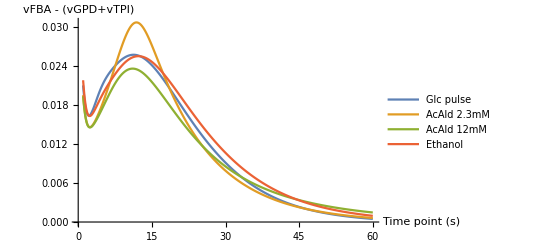

```mathematica
FBAvsGPDTPIplot=ListLinePlot[{MapThread[{#1,#2}&,{tList, vFBAvsvGPDvTPIGlcPulse}],
			MapThread[{#1,#2}&,{tList, vFBAvsvGPDvTPIAcAld1}],
			MapThread[{#1,#2}&,{tList, vFBAvsvGPDvTPIAcAld2}],
			MapThread[{#1,#2}&,{tList, vFBAvsvGPDvTPIEthanol}]},
PlotLegends->{"Glc pulse","AcAld 2.3mM","AcAld 12mM", "Ethanol"},
AxesLabel->{"Time point (s)","vFBA - (vGPD+vTPI)"},AxesOrigin->{0,0}]
```

```mathematica
Export["vFBA_-_vGPD+vTPI.pdf", FBAvsGPDTPIplot];
```

```mathematica
vFBAvsvGPDvTPIGlcPulseData = MapThread[{#1,#2, #3,#4, #5}&,{tList,vFBAvsvGPDvTPIGlcPulse,vFBAvsvGPDvTPIAcAld1, vFBAvsvGPDvTPIAcAld2 ,vFBAvsvGPDvTPIEthanol}];
Insert[vFBAvsvGPDvTPIGlcPulseData,{"t","glc_pulse", "glc_acald_2.3", "glc_acald_12","glc_ethanol"},1];
Export["vFBA_-_vGPD+vTPI_data.csv", vFBAvsvGPDvTPIGlcPulseData, "CSV"];
```

#### TPI - GAPDH

```mathematica
TPIvsGAPDHfluxGlcPulse = Table[Total[Values@FilterRules[fluxGlcPulse,{Subscript[v, TPI],Subscript[v, FBA]}]/.t-> tPoint]-Total[Values@FilterRules[fluxGlcPulse,{Subscript[v, TDH_TDH1],Subscript[v, TDH_TDH2],Subscript[v, TDH_TDH3]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
TPIvsGAPDHfluxAcAld1 = Table[Total[Values@FilterRules[fluxCoinjection1,{Subscript[v, TPI],Subscript[v, FBA]}]/.t-> tPoint]-Total[Values@FilterRules[fluxCoinjection1,{Subscript[v, TDH_TDH1],Subscript[v, TDH_TDH2],Subscript[v, TDH_TDH3]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
TPIvsGAPDHfluxAcAld2 = Table[Total[Values@FilterRules[fluxCoinjection2,{Subscript[v, TPI],Subscript[v, FBA]}]/.t-> tPoint]-Total[Values@FilterRules[fluxCoinjection2,{Subscript[v, TDH_TDH1],Subscript[v, TDH_TDH2],Subscript[v, TDH_TDH3]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
TPIvsGAPDHfluxEthanol = Table[Total[Values@FilterRules[fluxEthanolIncrease,{Subscript[v, TPI],Subscript[v, FBA]}]/.t-> tPoint]-Total[Values@FilterRules[fluxEthanolIncrease,{Subscript[v, TDH_TDH1],Subscript[v, TDH_TDH2],Subscript[v, TDH_TDH3]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
```

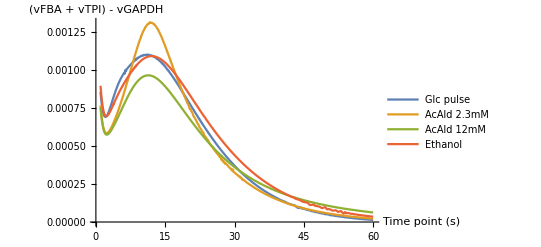

```mathematica
TPIvsGAPDHplot=ListLinePlot[{MapThread[{#1,#2}&,{tList, TPIvsGAPDHfluxGlcPulse}],
			MapThread[{#1,#2}&,{tList, TPIvsGAPDHfluxAcAld1}],
			MapThread[{#1,#2}&,{tList, TPIvsGAPDHfluxAcAld2}],
			MapThread[{#1,#2}&,{tList, TPIvsGAPDHfluxEthanol}]},
PlotLegends->{"Glc pulse","AcAld 2.3mM","AcAld 12mM", "Ethanol"},
AxesLabel->{"Time point (s)","(vFBA + vTPI) - vGAPDH"},AxesOrigin->{0,0}]
```

```mathematica
Export["vTPI_-_vGAPD.pdf", TPIvsGAPDHplot];
```

```mathematica
TPIvsGAPDHData = MapThread[{#1,#2, #3,#4, #5}&,{tList,TPIvsGAPDHfluxGlcPulse,TPIvsGAPDHfluxAcAld1, TPIvsGAPDHfluxAcAld2 ,TPIvsGAPDHfluxEthanol}];
Insert[TPIvsGAPDHData,{"t","glc_pulse", "glc_acald_2.3", "glc_acald_12","glc_ethanol"},1];
Export["vTPI_-_vGAPD_data.csv", TPIvsGAPDHData, "CSV"];
```

#### GAPDH - PGK

```mathematica
GAPDHvsPGKfluxGlcPulse = Table[Total[Values@FilterRules[fluxGlcPulse,{Subscript[v, TDH_TDH1],Subscript[v, TDH_TDH2],Subscript[v, TDH_TDH3]}]/.t-> tPoint]-(Values@FilterRules[fluxGlcPulse,{Subscript[v, PGK]}]/.t-> tPoint),
{tPoint,tList}]//Flatten;
GAPDHvsPGKfluxAcAld1 = Table[Total[Values@FilterRules[fluxCoinjection1,{Subscript[v, TDH_TDH1],Subscript[v, TDH_TDH2],Subscript[v, TDH_TDH3]}]/.t-> tPoint]-(Values@FilterRules[fluxCoinjection1,{Subscript[v, PGK]}]/.t-> tPoint),
{tPoint,tList}]//Flatten;
GAPDHvsPGKfluxAcAld2 = Table[Total[Values@FilterRules[fluxCoinjection2,{Subscript[v, TDH_TDH1],Subscript[v, TDH_TDH2],Subscript[v, TDH_TDH3]}]/.t-> tPoint]-(Values@FilterRules[fluxCoinjection2,{Subscript[v, PGK]}]/.t-> tPoint),
{tPoint,tList}]//Flatten;
GAPDHvsPGKfluxEthanol = Table[Total[Values@FilterRules[fluxEthanolIncrease,{Subscript[v, TDH_TDH1],Subscript[v, TDH_TDH2],Subscript[v, TDH_TDH3]}]/.t-> tPoint]-(Values@FilterRules[fluxEthanolIncrease,{Subscript[v, PGK]}]/.t-> tPoint),
{tPoint,tList}]//Flatten;
```

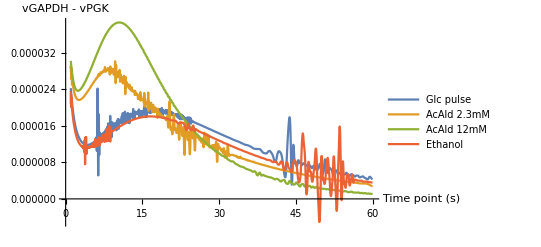

```mathematica
GAPDHvsPGKplot=ListLinePlot[{MapThread[{#1,#2}&,{tList, GAPDHvsPGKfluxGlcPulse}],
			MapThread[{#1,#2}&,{tList, GAPDHvsPGKfluxAcAld1}],
			MapThread[{#1,#2}&,{tList, GAPDHvsPGKfluxAcAld2}],
			MapThread[{#1,#2}&,{tList, GAPDHvsPGKfluxEthanol}]},
PlotLegends->{"Glc pulse","AcAld 2.3mM","AcAld 12mM", "Ethanol"},
AxesLabel->{"Time point (s)","vGAPDH - vPGK"},AxesOrigin->{0,0}]
```

```mathematica
Export["vGAPD_-_vPGK_.pdf", GAPDHvsPGKplot];
```

```mathematica
GAPDHvsPGKData = MapThread[{#1,#2, #3,#4, #5}&,{tList,GAPDHvsPGKfluxGlcPulse,GAPDHvsPGKfluxAcAld1, GAPDHvsPGKfluxAcAld2 ,GAPDHvsPGKfluxEthanol}];
Insert[GAPDHvsPGKData,{"t","glc_pulse", "glc_acald_2.3", "glc_acald_12","glc_ethanol"},1];
Export["vGAPD_-_vPGK_data.csv", GAPDHvsPGKData, "CSV"];
```

#### PGK-GPM

```mathematica
PGKvsGPMfluxGlcPulse = Table[(Values@FilterRules[fluxGlcPulse,{Subscript[v, PGK]}]/.t-> tPoint)-(Values@FilterRules[fluxGlcPulse,{Subscript[v, GPM]}]/.t-> tPoint),
{tPoint,tList}]//Flatten;
PGKvsGPMfluxAcAld1 = Table[(Values@FilterRules[fluxCoinjection1,{Subscript[v, PGK]}]/.t-> tPoint)-(Values@FilterRules[fluxCoinjection1,{Subscript[v, GPM]}]/.t-> tPoint),
{tPoint,tList}]//Flatten;
PGKvsGPMfluxAcAld2 = Table[(Values@FilterRules[fluxCoinjection2,{Subscript[v, PGK]}]/.t-> tPoint)-(Values@FilterRules[fluxCoinjection2,{Subscript[v, GPM]}]/.t-> tPoint),
{tPoint,tList}]//Flatten;
PGKvsGPMfluxEthanol = Table[(Values@FilterRules[fluxEthanolIncrease,{Subscript[v, PGK]}]/.t-> tPoint)-(Values@FilterRules[fluxEthanolIncrease,{Subscript[v, GPM]}]/.t-> tPoint),
{tPoint,tList}]//Flatten;
```

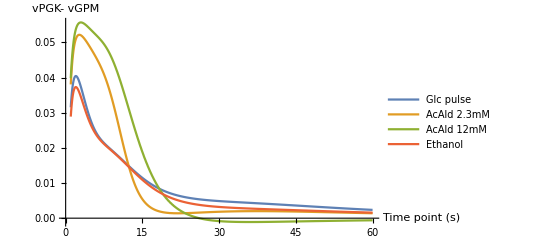

```mathematica
PGKvsGPMplot=ListLinePlot[{MapThread[{#1,#2}&,{tList, PGKvsGPMfluxGlcPulse}],
			MapThread[{#1,#2}&,{tList, PGKvsGPMfluxAcAld1}],
			MapThread[{#1,#2}&,{tList, PGKvsGPMfluxAcAld2}],
			MapThread[{#1,#2}&,{tList, PGKvsGPMfluxEthanol}]},
PlotLegends->{"Glc pulse","AcAld 2.3mM","AcAld 12mM", "Ethanol"},
AxesLabel->{"Time point (s)","vPGK- vGPM"},AxesOrigin->{0,0}]
```

```mathematica
Export["vPGK_-_vGPM.pdf", PGKvsGPMplot];
```

```mathematica
PGKvsGPMData = MapThread[{#1,#2, #3,#4, #5}&,{tList,PGKvsGPMfluxGlcPulse,PGKvsGPMfluxAcAld1, PGKvsGPMfluxAcAld2 ,PGKvsGPMfluxEthanol}];
Insert[PGKvsGPMData,{"t","glc_pulse", "glc_acald_2.3", "glc_acald_12","glc_ethanol"},1];
Export["vPGK_-_vGPM_data.csv", PGKvsGPMData, "CSV"];
```

#### GPM - ENO

```mathematica
GPMvsENOfluxGlcPulse = Table[(Values@FilterRules[fluxGlcPulse,{Subscript[v, GPM]}]/.t-> tPoint)-Total[Values@FilterRules[fluxGlcPulse,{Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
GPMvsENOfluxAcAld1 = Table[(Values@FilterRules[fluxCoinjection1,{Subscript[v, GPM]}]/.t-> tPoint)-Total[Values@FilterRules[fluxCoinjection1,{Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
GPMvsENOfluxAcAld2 = Table[(Values@FilterRules[fluxCoinjection2,{Subscript[v, GPM]}]/.t-> tPoint)-Total[Values@FilterRules[fluxCoinjection2,{Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
GPMvsENOfluxEthanol = Table[(Values@FilterRules[fluxEthanolIncrease,{Subscript[v, GPM]}]/.t-> tPoint)-Total[Values@FilterRules[fluxEthanolIncrease,{Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
```

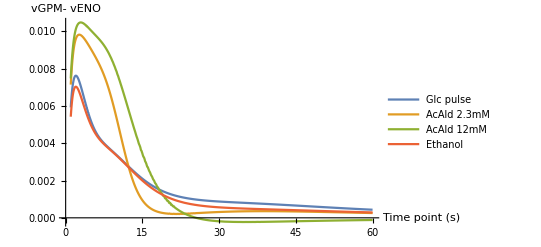

```mathematica
GPMvsENOplot=ListLinePlot[{MapThread[{#1,#2}&,{tList, GPMvsENOfluxGlcPulse}],
			MapThread[{#1,#2}&,{tList, GPMvsENOfluxAcAld1}],
			MapThread[{#1,#2}&,{tList, GPMvsENOfluxAcAld2}],
			MapThread[{#1,#2}&,{tList, GPMvsENOfluxEthanol}]},
PlotLegends->{"Glc pulse","AcAld 2.3mM","AcAld 12mM", "Ethanol"},
AxesLabel->{"Time point (s)","vGPM- vENO"},AxesOrigin->{0,0}]
```

```mathematica
Export["vGPM_-_vENO.pdf", GPMvsENOplot];
```

```mathematica
GPMvsENOData = MapThread[{#1,#2, #3,#4, #5}&,{tList,GPMvsENOfluxGlcPulse,GPMvsENOfluxAcAld1, GPMvsENOfluxAcAld2 ,GPMvsENOfluxEthanol}];
Insert[GPMvsENOData,{"t","glc_pulse", "glc_acald_2.3", "glc_acald_12","glc_ethanol"},1];
Export["vGPM_-_vENO_data.csv", GPMvsENOData, "CSV"];
```

#### ENO-PYK

```mathematica
ENOvsPYKfluxGlcPulse = Table[Total[Values@FilterRules[fluxGlcPulse,{Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2]}]/.t-> tPoint]-Total[Values@FilterRules[fluxGlcPulse,{Subscript[v, PYK_CDC19],Subscript[v, PYK_PYK2]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
ENOvsPYKfluxAcAld1 = Table[Total[Values@FilterRules[fluxCoinjection1,{Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2]}]/.t-> tPoint]-Total[Values@FilterRules[fluxCoinjection1,{Subscript[v, PYK_CDC19],Subscript[v, PYK_PYK2]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
ENOvsPYKfluxAcAld2 = Table[Total[Values@FilterRules[fluxCoinjection2,{Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2]}]/.t-> tPoint]-Total[Values@FilterRules[fluxCoinjection2,{Subscript[v, PYK_CDC19],Subscript[v, PYK_PYK2]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
ENOvsPYKfluxEthanol = Table[Total[Values@FilterRules[fluxEthanolIncrease,{Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2]}]/.t-> tPoint]-Total[Values@FilterRules[fluxEthanolIncrease,{Subscript[v, PYK_CDC19],Subscript[v, PYK_PYK2]}]/.t-> tPoint],
{tPoint,tList}]//Flatten;
```

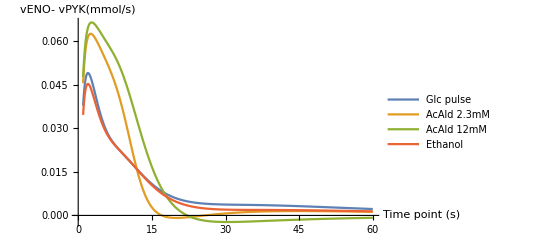

```mathematica
ENOvsPYKplot=ListLinePlot[{MapThread[{#1,#2}&,{tList, ENOvsPYKfluxGlcPulse}],
			MapThread[{#1,#2}&,{tList, ENOvsPYKfluxAcAld1}],
			MapThread[{#1,#2}&,{tList, ENOvsPYKfluxAcAld2}],
			MapThread[{#1,#2}&,{tList, ENOvsPYKfluxEthanol}]},
PlotLegends->{"Glc pulse","AcAld 2.3mM","AcAld 12mM", "Ethanol"},
AxesLabel->{"Time point (s)","vENO- vPYK(mmol/s)"},AxesOrigin->{0,0}]
```

```mathematica
Export["vENO_-_vPYK.pdf", ENOvsPYKplot];
```

```mathematica
ENOvsPYKData = MapThread[{#1,#2, #3,#4, #5}&,{tList,ENOvsPYKfluxGlcPulse,ENOvsPYKfluxAcAld1, ENOvsPYKfluxAcAld2 ,ENOvsPYKfluxEthanol}];
Insert[ENOvsPYKData,{"t","glc_pulse", "glc_acald_2.3", "glc_acald_12","glc_ethanol"},1];
Export["vENO_-_vPYK_data.csv", ENOvsPYKData, "CSV"];
```

### Exponential decay

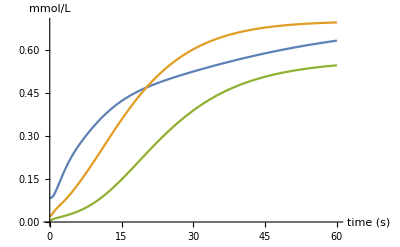

```mathematica
P3Gdata = Values[FilterRules[concentrationGlcPulse,P3G^cell]]/.t-> Range[0,60,0.01];
DHAPdata = Values[FilterRules[concentrationGlcPulse,DHAP^cell]]/.t-> Range[0,60,0.01];
FBPdata = Values[FilterRules[concentrationGlcPulse,F16bP^cell]]/.t-> Range[0,60,0.01];
origPlot=ListLinePlot[{MapThread[{#1, #2}&,{Range[0,60,0.01],P3Gdata[[1]]}],
			MapThread[{#1, #2}&,{Range[0,60,0.01],DHAPdata[[1]]}],
			MapThread[{#1, #2}&,{Range[0,60,0.01],FBPdata[[1]]}]},
AxesLabel-> {"time (s)", "mmol/L"}]
```

```mathematica
Export["original_plot_3PG_DHAP_FBP.pdf", origPlot];
```

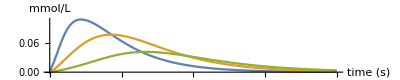

```mathematica
tau=5;
tauDelay1=3;
tauDelay2=5;
tauDelay3=7;
P3Gdata = Values[FilterRules[concentrationGlcPulse,P3G^cell]]*(1-Exp[(-t/tauDelay1)])*Exp[(-t/(tau+tauDelay1))]/.t-> Range[0,60,0.01];
DHAPdata = Values[FilterRules[concentrationGlcPulse,DHAP^cell]]*(1-Exp[(-t/tauDelay2)])*Exp[(-t/(tau+tauDelay2))]/.t-> Range[0,60,0.01];
FBPdata = Values[FilterRules[concentrationGlcPulse,F16bP^cell]]*(1-Exp[(-t/tauDelay3)])*Exp[(-t/(tau+tauDelay3))]/.t-> Range[0,60,0.01];
decayPlot=ListLinePlot[{MapThread[{#1, #2}&,{Range[0,60,0.01],P3Gdata[[1]]}],
			MapThread[{#1, #2}&,{Range[0,60,0.01],DHAPdata[[1]]}],
			MapThread[{#1, #2}&,{Range[0,60,0.01],FBPdata[[1]]}]},			
 PlotRange->{{0,60},Full}, AspectRatio->1/5, PlotLegends->{"P3G", "DHAP", "F16bP"}, AxesLabel-> {"time (s)", "mmol/L"}]
```

```mathematica
Export["decay_plot_3PG_DHAP_FBP.pdf", decayPlot];
```

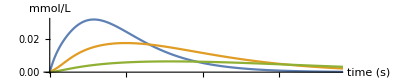

```mathematica
tau=0.0001;
tauDelay1=2;
tauDelay2=3;
tauDelay3=4;
P3Gdata = Values[FilterRules[concentrationGlcPulse,P3G^cell]]*(1-Exp[(-t/tauDelay1)])*Exp[(-t/(tau+tauDelay1))]/.t-> Range[0,60,0.01];
DHAPdata = Values[FilterRules[concentrationGlcPulse,DHAP^cell]]*(1-Exp[(-t/tauDelay2)])*Exp[(-t/(tau+tauDelay2))]/.t-> Range[0,60,0.01];
FBPdata = Values[FilterRules[concentrationGlcPulse,F16bP^cell]]*(1-Exp[(-t/tauDelay3)])*Exp[(-t/(tau+tauDelay3))]/.t-> Range[0,60,0.01];
decayPlot=ListLinePlot[{MapThread[{#1, #2}&,{Range[0,60,0.01],P3Gdata[[1]]}],
			MapThread[{#1, #2}&,{Range[0,60,0.01],DHAPdata[[1]]}],
			MapThread[{#1, #2}&,{Range[0,60,0.01],FBPdata[[1]]}]},			
 PlotRange->{{0,15},Full}, AspectRatio->1/5, PlotLegends->{"P3G", "DHAP", "F16bP"}, AxesLabel-> {"time (s)", "mmol/L"}]
```

```mathematica
Export["decay_plot_3PG_DHAP_FBP_15s.pdf", decayPlot];
```